## 3.029 Spring 2022 Lecture 22 - 04/25/2022

## Order - Disorder Transition

Recall that in our regular-activity solution model, we assume component interactions to be pairwise:

Today, we’ll code up a lattice-Kinetic Monte Carlo method for the regular solution model to investigate the competition between enthalpy and entropy visually

We’ll consider a two-component system:

(red) A atoms

occupying a lattice site with an A atom “costs” an energy E_A

(blue) B atoms

occupying a lattice site with a B atom “costs” an energy E_B

as well as (white) vacancies

which have a site energy, E_V equal to zero

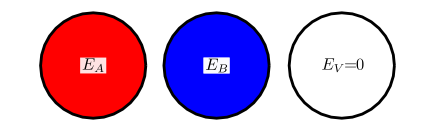

We’ll also consider the following pairwise interactions

E_AA : the energy associated with an A—A pair

E_BB : the energy associated with an B—B pair

E_AB :  the energy associated with an A—B pair

Notes:

Pairwise “interactions” with empty vacancy sites cost no energy

We can use a “weight” α  to denote interactions of second nearest-neighbors

Site energies:

EA: the energy of a site occupied by A

EB: the energy of a site occupied by B

## Step-By-Step Simulation

Let’s start by generating an  square grid, with a random configuration of red, blue, and white sites

given some initial composition fractions

Remember we can use `RandomChoice` to obtain a weighted random choice

We’ll represent vacancies using 0, A atoms using 1, and B atoms using 2

```mathematica
Clear[randomLattice]
randomLattice[{n_,m_},{fA_,fB_,fV_:0.},seedRandom_|PatternSequence[]]:=With[{s=SeedRandom[seedRandom]},RandomChoice[{fV,fA,fB}->{0,1,2},{m,n}]]
```

```mathematica
Grid[
randomLattice[{30,10},{0.475,0.475,0.05},3029]
]
```

1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 0 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1
2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2
1 | 1 | 2 | 2 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 0 | 1 | 1 | 2 | 1
1 | 1 | 1 | 1 | 2 | 0 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 1
1 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 0 | 1
2 | 2 | 0 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 1 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 1
0 | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 1 | 1 | 0 | 2 | 1 | 2
0 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 1 | 2 | 2 | 0 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 0 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 0 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 1

And write a simple function to visualize the current state

```mathematica
visualizeLatticeRaster[state_]:=ArrayPlot[state,
ColorRules->{0->White,1->Red,2->Blue},
Frame->False,PlotRangePadding->None,DataReversed->True,ImageSize->500]
```

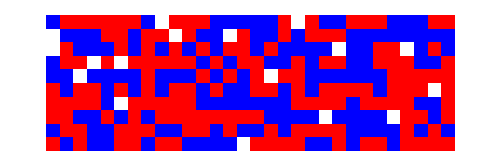

```mathematica
visualizeLatticeRaster[randomLattice[{30,10},{0.475,0.475,0.05},3029]]
```

In-fact we can do better using Graphics objects

```mathematica
visualizeLattice[state_]:=Block[{posA,posB,posV},
{posV,posA,posB}=Position[state,#,{2},Heads->False]&/@{0,1,2};
Graphics[MapThread[{EdgeForm[Black],FaceForm[#1],Table[Disk[Reverse[i],1/2],{i,#2}]}&,{{White,Red,Blue},{posV,posA,posB}}]
,PlotRangePadding->None,ImageSize->500]
]
```

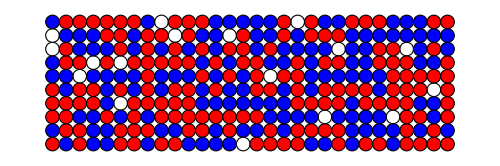

```mathematica
visualizeLattice[randomLattice[{30,10},{0.475,0.475,0.05},3029]]
```

Next, we want to be able to evaluate the total energy of a given state

Remember, we’ll consider up to second nearest neighbor interactions

This means that for each site we need to compute what is known as a 3x3 Moore neighborhood

Note: we briefly talked about this in one of our first code-show-and tells on Cellular Automata, see here

We’ll make use of vectorization to do this efficiently

That is, we’ll “rotate” our lattice according to all our neighborhood directions

making a 3D array with dimensions (number_of_neighbors, m,n)

And then operate on this 3D array in “one pass”

Let’s see this using a simple 1D lattice

note this implies periodic boundary conditions - which works well in our case

```mathematica
Range[10]
RotateRight[Range[10],1]
RotateRight[Range[10],-1]
```

{1,2,3,4,5,6,7,8,9,10}

{10,1,2,3,4,5,6,7,8,9}

{2,3,4,5,6,7,8,9,10,1}

and analogously in 2D

```mathematica
Array[Subscript[x,#1,#2]&,{3,3}]//Grid
```

x_(1,1) | x_(1,2) | x_(1,3)
x_(2,1) | x_(2,2) | x_(2,3)
x_(3,1) | x_(3,2) | x_(3,3)

```mathematica
RotateRight[Array[Subscript[x,#1,#2]&,{3,3}],{0,1}]//Grid
```

x_(1,3) | x_(1,1) | x_(1,2)
x_(2,3) | x_(2,1) | x_(2,2)
x_(3,3) | x_(3,1) | x_(3,2)

The following function allows us to apply a function on each cell by passing its 3x3 neighborhood as arguments

```mathematica
moore3by3Neighborhood={{0,0},{1,0},{0,-1},{-1,0},{0,1},{1,-1},{-1,-1},{-1,1},{1,1}};
mooreNeighborhood[function__,lattice_,neighbors_:moore3by3Neighborhood]:=MapThread[function,Map[RotateRight[lattice,#]&,neighbors],2];
```

E.g. for a symbolic 4 x 4 lattice and a generic function f

```mathematica
mooreNeighborhood[f,Array[Subscript[x,#1,#2]&,{4,4}]]
```

{{f[x_(1,1),x_(4,1),x_(1,2),x_(2,1),x_(1,4),x_(4,2),x_(2,2),x_(2,4),x_(4,4)],f[x_(1,2),x_(4,2),x_(1,3),x_(2,2),x_(1,1),x_(4,3),x_(2,3),x_(2,1),x_(4,1)],f[x_(1,3),x_(4,3),x_(1,4),x_(2,3),x_(1,2),x_(4,4),x_(2,4),x_(2,2),x_(4,2)],f[x_(1,4),x_(4,4),x_(1,1),x_(2,4),x_(1,3),x_(4,1),x_(2,1),x_(2,3),x_(4,3)]},{f[x_(2,1),x_(1,1),x_(2,2),x_(3,1),x_(2,4),x_(1,2),x_(3,2),x_(3,4),x_(1,4)],f[x_(2,2),x_(1,2),x_(2,3),x_(3,2),x_(2,1),x_(1,3),x_(3,3),x_(3,1),x_(1,1)],f[x_(2,3),x_(1,3),x_(2,4),x_(3,3),x_(2,2),x_(1,4),x_(3,4),x_(3,2),x_(1,2)],f[x_(2,4),x_(1,4),x_(2,1),x_(3,4),x_(2,3),x_(1,1),x_(3,1),x_(3,3),x_(1,3)]},{f[x_(3,1),x_(2,1),x_(3,2),x_(4,1),x_(3,4),x_(2,2),x_(4,2),x_(4,4),x_(2,4)],f[x_(3,2),x_(2,2),x_(3,3),x_(4,2),x_(3,1),x_(2,3),x_(4,3),x_(4,1),x_(2,1)],f[x_(3,3),x_(2,3),x_(3,4),x_(4,3),x_(3,2),x_(2,4),x_(4,4),x_(4,2),x_(2,2)],f[x_(3,4),x_(2,4),x_(3,1),x_(4,4),x_(3,3),x_(2,1),x_(4,1),x_(4,3),x_(2,3)]},{f[x_(4,1),x_(3,1),x_(4,2),x_(1,1),x_(4,4),x_(3,2),x_(1,2),x_(1,4),x_(3,4)],f[x_(4,2),x_(3,2),x_(4,3),x_(1,2),x_(4,1),x_(3,3),x_(1,3),x_(1,1),x_(3,1)],f[x_(4,3),x_(3,3),x_(4,4),x_(1,3),x_(4,2),x_(3,4),x_(1,4),x_(1,2),x_(3,2)],f[x_(4,4),x_(3,4),x_(4,1),x_(1,4),x_(4,3),x_(3,1),x_(1,1),x_(1,3),x_(3,3)]}}

```mathematica
Clear[energyState]
energyState[{eA_,eB_},{eAA_,eBB_,eAB_},α_][0,neighs__]:=0

energyState[{eA_,eB_},{eAA_,eBB_,eAB_},α_][1,neighs__]:=energyState[{eA,eB},{eAA,eBB,eAB},α][1,neighs]=Block[{nn,nnn,nnCounts,nnnCounts},

{nn,nnn}=TakeList[{neighs},{4,4}];
nnCounts=BinCounts[nn,{0,3,1}];
nnnCounts=BinCounts[nnn,{0,3,1}];

eA + nnCounts.{0,eAA,eAB}+ nnnCounts.{0,eAA,eAB} α

]

energyState[{eA_,eB_},{eAA_,eBB_,eAB_},α_][2,neighs__]:=energyState[{eA,eB},{eAA,eBB,eAB},α][2,neighs]=Block[{nn,nnn,nnCounts,nnnCounts},

{nn,nnn}=TakeList[{neighs},{4,4}];
nnCounts=BinCounts[nn,{0,3,1}];
nnnCounts=BinCounts[nnn,{0,3,1}];

eB + nnCounts .{0,eAB,eBB}+ nnnCounts.{0,eAB,eBB} α

]
```

Let’s check this visually

```mathematica
MatrixForm[randomLattice[{4,4},{0.475,0.475,0.05},3029]]
```

(1 | 2 | 1 | 2
2 | 1 | 1 | 2
1 | 1 | 2 | 2
2 | 2 | 0 | 1)

```mathematica
MatrixForm[
mooreNeighborhood[energyState[{eA,eB},{eAA,eBB,eAB},α],randomLattice[{4,4},{0.475,0.475,0.05},3029]]
]
```

(eA+4 eAB+(2 eAA+2 eAB) α | 3 eAB+eB+eBB+(eAB+2 eBB) α | eA+eAA+2 eAB+(2 eAA+2 eAB) α | 3 eAB+eB+eBB+(eAB+2 eBB) α
3 eAB+eB+eBB+(eAB+3 eBB) α | eA+2 eAA+2 eAB+(3 eAA+eAB) α | eA+2 eAA+2 eAB+(eAA+3 eAB) α | eAB+eB+3 eBB+(3 eAB+eBB) α
eA+eAA+3 eAB+(2 eAA+2 eAB) α | eA+2 eAA+2 eAB+(eAA+2 eAB) α | 2 eAB+eB+eBB+(2 eAB+2 eBB) α | 2 eAB+eB+2 eBB+(eAB+2 eBB) α
3 eAB+eB+eBB+(eAB+3 eBB) α | eAB+eB+2 eBB+(3 eAB+eBB) α | 0 | eA+3 eAB+(3 eAA+eAB) α)

Notice we also used our familiar “memoization” trick to speed this up

there’s only a finite number of neighbor configurations so we should be able to very quickly exhaust them all

We also need a routine to randomly select a vacancy, and swap it with one of its neighbors

```mathematica
swapRandomVacancy[lattice_]:=Block[{state=lattice,posV,randomDirection,newV,dims=Dimensions[lattice]},

posV=RandomChoice[Position[state,0,{2},Heads->False]];
randomDirection=RandomChoice[Rest[moore3by3Neighborhood]];
newV=Mod[posV+randomDirection,dims,1];

{state[[posV[[1]],posV[[2]]]],state[[newV[[1]],newV[[2]]]]}={state[[newV[[1]],newV[[2]]]],state[[posV[[1]],posV[[2]]]]};
state
]
```

```mathematica
visualizeLattice[randomLattice[{30,10},{0.475,0.475,0.05},3029]]
```

-Graphics-

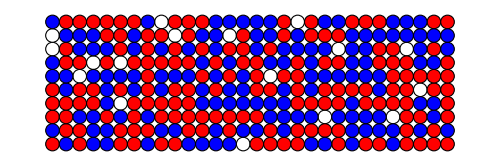

```mathematica
visualizeLattice[swapRandomVacancy[randomLattice[{30,10},{0.475,0.475,0.05},3029]]]
```

We then proceed to write our standard metropolis algorithm routine

```mathematica
monteCarloStep[{eA_,eB_},{eAA_,eBB_,eAB_},α_][temperature_][lattice_]:=Block[{latticeAfter,energyBefore,deltaEnergy,probability},
energyBefore=Total[mooreNeighborhood[energyState[{eA,eB},{eAA,eBB,eAB},α],lattice],2];

latticeAfter=swapRandomVacancy[lattice];
deltaEnergy=Total[mooreNeighborhood[energyState[{eA,eB},{eAA,eBB,eAB},α],latticeAfter],2]-energyBefore;

If[deltaEnergy<= 0, Return[latticeAfter]];

probability = Exp[-deltaEnergy/temperature];
RandomChoice[{probability,1-probability}->{latticeAfter,lattice}]

]
```

And run the simulation dynamically

```mathematica
lattice=randomLattice[{30,10},{0.475,0.475,0.05},3029];
Dynamic[visualizeLattice[lattice]]
```

```mathematica
Do[lattice=monteCarloStep[{1,1},{-2,-2,2},1][2][lattice],10000]
```

What if we wanted to simulate the effects of a finite system, i.e. a surface?

How would we change our simulation to account for this?

## Order-Disorder Transformation Demo

The above was very easy to set-up, and runs fairly fast

but we can do better by compiling the time-consuming energy-computation step

This is what the source code below does

We’ll use this to explore the physics in more detail

In particular, we’ll investigate the effects of surfaces using a finite-size system

Which is in-contact with A-atoms and B-atoms vapor-pressure

To do this we need to introduce chemical potentials for the two species

Intuitively, the chemical potential of species A is the “total” energy difference between placing an A atom on a lattice from the vapor, as opposed to placing a vacancy

Recall that the chemical potential of a species cannot be defined solely on a lattice, but instead is given by the difference of the species and a vacancy

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"lattice_order_disorder_source.m"}]];
```

```mathematica
(*orderdisorderSimulation[μB,μR,eAA,eAB][{vFrac,bFrac,rFrac}]*)
orderdisorderSimulation[0,0,0,0][{0.1,0.45,0.45}]
```

mvfpi_shm35FrontEndObject[LinkObject["mvfpi_shm", 3, 1]]35Untitled-9

### Spinodal Decomposition

Negative (favourable) like interactions

Species phase-separate

left/right bulk ground state

Vacancies accumulate at surfaces

Vacancies act as a surfactant lowering the surface energy (on-site energy zero)

### Ordered - Unfavourable

Negative (favourable) like and positive (unfavourable) unlike interactions

Ordering transformation

Stripes ground state

### Ordered - Favourable

Positive (unfavourable) like and negative (favourable) unlike interactions

Ordering transformation

Checkerboard ground state

### Effect of Chemical Potential

Start at zero interactions

turn off constant composition

Make like interactions favourable

will phase-separate

vacancies will leave the systems

remaining vacancies trapped along domain interfaces

very much exaggerated

Increase species A chemical potential

high vapor pressure means it’s trying to “force” A-atoms from vapour in to lattice

Decrease species B chemical potential

low vapor pressure means it’s trying to “force” B-atoms from the lattice into the vapour

however, if species B is “trapped” inside the lattice, it’s hard to diffuse out to the surface

this is a very real materials-science phenomenon!